# Reference count: pubyear: 1946 - 1950

## File

```mathematica
workdir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

```mathematica
filelisttxt="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/reflist_filenames.txt"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/reflist_filenames.txt

```mathematica
filelist=StringSplit[Import[filelisttxt,"String"]]
```

{reflistBypubyear_163-167.wl,reflistBypubyear_168-172.wl,reflistBypubyear_173-177.wl,reflistBypubyear_178-182.wl,reflistBypubyear_183-187.wl,reflistBypubyear_188-192.wl,reflistBypubyear_193-197.wl,reflistBypubyear_198-202.wl,reflistBypubyear_203-207.wl,reflistBypubyear_208-212.wl,reflistBypubyear_213-217.wl,reflistBypubyear_218-222.wl,reflistBypubyear_223-227.wl,reflistBypubyear_228-232.wl,reflistBypubyear_233-237.wl}

```mathematica
timespan="1946-1950"
```

1946-1950

## Import

```mathematica
SetDirectory[workdir]
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference

reference count

```mathematica
(e[1950]=Get[filelist[[1]]])//Length
```

33832

## Stat

### Ref edge

Edge : {"citingPMID" -> "citedPMID"}

reference count

```mathematica
e[1950,"reference count"]=e[1950]//Length
```

33832

citing article count

```mathematica
(e[1950,"citing art count"]=Sort[Tally[e[1950],#1[[1]]==#2[[1]]&],#1[[2]]>=#2[[2]]&])//Length
```

10389

cited article count

```mathematica
(e[1950,"cited art count"]=Sort[Tally[e[1950],#1[[2]]==#2[[2]]&],#1[[2]]>=#2[[2]]&])//Length
```

18495

: cited count ordered

```mathematica
e[1950,"cited count ordered"]=Map[#[[2]]&,e[1950,"cited art count"]];
```

:: 1 percent count

```mathematica
e[1950,"reference count"]/100//N
```

338.32

::: top 1 percent position

```mathematica
topCitedPercentPos[1950]=Min[Nearest[Accumulate[e[1950,"cited count ordered"]]->"Index",e[1950,"reference count"]/100]]
```

10

:::: top 1 percent cited articles

```mathematica
topCitedArt1Perc[1950,"cited art count"]=e[1950,"cited art count"][[1;;topCitedPercentPos[1950]]]
```

{{16747969→16747784,74},{16561086→17247100,35},{16748022→16747456,32},{16695331→16694558,31},{16695354→16694480,29},{16747954→16747508,28},{16695476→16695228,28},{16561086→17247150,27},{18016456→18016252,26},{19108094→17751251,26}}

```mathematica
topCitedArt1Perc[1950,"PMID"]=Map[#[[1,2]]&,topCitedArt1Perc[1950,"cited art count"]]
```

{16747784,17247100,16747456,16694558,16694480,16747508,16695228,17247150,18016252,17751251}

:::: top 1 percent citing/cited articles

```mathematica
(topCitingCitedArt1Perc[1950,"citing rule"]=Map[Cases[e[1950],Rule[x_,y_]/;y==#]&,topCitedArt1Perc[1950,"PMID"]])//Length
```

10

:::: top 1 percent cited theme (MeSH)

Another nb

:::: top 1 percent citing theme (MeSH)

Another nb

### Zipf

: rank vs. count

```mathematica
e[1950,"plot count points"]=(e[1950,"plot count"]=Map[#[[2]]&,e[1950,"cited art count"]])//Length
```

18495

:: fitting to Zipf

```mathematica
zipf[r_]:=c r^(-a)
```

```mathematica
Clear[{c,a}]
zipfParam[1950]=FindFit[e[1950,"plot count"],zipf[x],{c,a},x]
```

{c→78.765,a→0.433125}

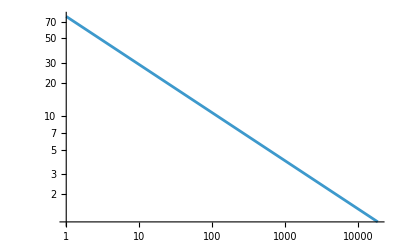

```mathematica
grx=LogLogPlot[zipf[x]/.zipfParam[1950],{x,1,e[1950,"plot count points"]},PlotRange->Full]
```

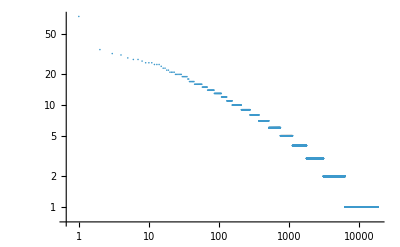

```mathematica
gry=ListLogLogPlot[e[1950,"plot count"],PlotRange->Full]
```

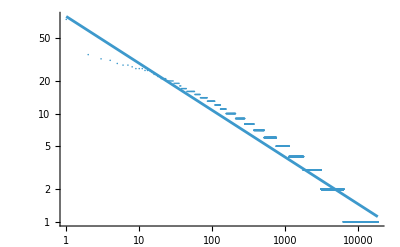

```mathematica
Show[{gry,grx},PlotRange->Full]
```

### Save

```mathematica
(*DeleteFile[workdir<>timespan<>"_CitingCitedArtCount.save"]*)
(*Save[workdir<>timespan<>"_CitingCitedArtCount.save",e]*)
```

DeleteFile::fdnfnd: ディレクトリまたはファイル/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_CitingCitedArtCount.saveが見付かりませんでした．

$Failed

```mathematica
(*DeleteFile[workdir<>timespan<>"_topCitingCitedArt1Perc.save"]*)
(*Save[workdir<>timespan<>"_topCitingCitedArt1Perc.save",topCitingCitedArt1Perc]*)
```